```mathematica
(*This AppendTo function wiss change the $Path to where we need to run the files.*)
SetDirectory[NotebookDirectory[]]
AppendTo[$Path,FileNameJoin[{Directory[],"mFiles/Multipole_Method"}]];
(*Cass the package that needs to be run!*)
Get["geometry.m"];
Needs["geometry`"];
```

```mathematica
"/Users/mahdiyeh/OneDrive - Imperial Cossege London/Mahdieh/Simulation/DCD_Package_Mathematica"
```

FilePath = /Users/mahdiyeh/OneDrive - Imperial College London/Mahdieh/Simulation/DCD_Package_Mathematica

geometry

Or Use

```mathematica
AppendTo[$Path,FileNameJoin[{"/Users/mahdiyeh/OneDrive - Imperial Cossege London/Mahdieh/DCD_Package","mFiles"}]];
Get["geometry.m"];
Needs["geometry`"];
```

```mathematica
"/Users/mahdiyeh/OneDrive - Imperial Cossege London/Mahdieh/DCD_Package"
```

FilePath = /Users/mahdiyeh/OneDrive - Imperial College London/Mahdieh/DCD_Package

geometry

```mathematica
Import["geometry.m"];
```

FilePath = /Users/mahdiyeh/OneDrive - Imperial College London/Mahdieh/DCD_Package

geometry

```mathematica
Get["geometry.m"];
Needs["geometry`"];
```

FilePath = /Users/mahdiyeh/OneDrive - Imperial College London/Mahdieh/DCD_Package

geometry

```mathematica
num1
```

1

```mathematica
$Path
```

```mathematica
"/Users/mahdiyeh/OneDrive - Imperial Cossege London/Mahdieh/Simulation/DCD_Package_Mathematica"
```

FilePath = /Users/mahdiyeh/OneDrive - Imperial College London/Mahdieh/Simulation/DCD_Package_Mathematica

geometry

```mathematica
ClearAss[listaa,listaaminus,listbb,listbbminus]
```

```mathematica
aa[q_]:=Module[{f}, f=Exp[-I Theta[q]](dd[q]/(16 Mu0))(s11+s22)]

bbm[q_] :=Module[{f}, f= aa[q]v0[1]^(-2) +  Exp[I Theta[q]](dd[q]/(8 Mu0))(s22-s11 + 2 I s12)]

(*"faraa"*)
faraa[q_]  := Module[{f}, f= Table[If[i ==1&&q<= ntot, Exp[-I Theta[q]](dd[q]/(16  Mu0))(s11+s22),0],{i,1,n}]]

(*"farbbminus"*)
farbbminus[q_]:= Module[{f, f1, f2, f3,f4}, 
f1=Exp[-I Theta[q]](dd[q]/(16*Mu0))(s11+s22);
f2= f1 v0[q]^(-2) +  Exp[I Theta[q]](dd[q]/(8*Mu0))(s22-s11 + 2 I s12) ;
f= Table[If[i ==1&&q<= ntot, f2,0],{i,1,n}]]
```

```mathematica
(*"faraaminus"*)
r5[q_]  := Module[{f}, f= faraa[q]]
faraaminus[q_]:=Module[{f},f=r5[q]]

(*"farbb"*)
farbb[q_] := Module[{f}, f= Table[ farbbminus[q][[i]] + 2 i Sinh[2*Zeta0[q]] faraa[q][[i]],{i,1,n}]]

listaa[q_]  := Module[{f},f= Table[faraa[q][[i]] , {i,n}]]
 listaaminus[q_] := Module[{f},f=listaa[q]]

listbbminus[q_]  := Module[{f},f= Table[farbbminus[q][[i]] , {i,n}]]
listbb[q_] := Module[{f},f= Table[farbb[q][[i]], {i,n}]]
(*"-----------VECTOR OF BOUNDARY CONDITIONS--------------"*)
```

```mathematica
ClearAss[bcf1, bcf2, bcf3, bcf,bc]

bcf1[i_, j_,q_] := Module[{f,f1,f2},
f1=f= -Chi0 listaa[q][[j]] + v0[q]^(2 j)Conjugate[listbbminus[q][[j]]];
f2=f1+TempratureInteraction1[q,j];
f= If[TS==0,f1,f2];
If[i == 1,f,0]
]

bcf2[i_, j_,q_] := Module[{f,f1,f2},
f1 =Chi0 v0[q]^(2j) listaaminus[q][[j]]- Conjugate[listbb[q][[j]]];
f2= f1 +TempratureInteraction2[q,j];
f= If[TS==0,f1,f2];
If[i == 2,f,0]
]

bcf3[i_, j_,q_] := Module[{f},If[i == 3,f =-listaa[q][[j]] - v0[q]^(2 j) Conjugate[listbbminus[q][[j]]],0]
]

bcf4[i_, j_,q_] := Module[{f},If[i == 4,f =- v0[q]^(2 j) listaaminus[q][[j]] - Conjugate[listbb[q][[j]]],0]
]

bcf[i_, j_,q_]:= Module[{f}, f =( bcf1[i,j,q]+ bcf2[i,j,q]+bcf3[i,j,q]+bcf4[i,j,q])]

ClearAss[bbc]

bbc[j_,q_]:=Module[{f}, f=Table[bcf[j,i,q], {k,1},{i,n}]]
Clear[bc]
```

```mathematica
bc[q_] :=Module[{f}, f=Table[bbc[i,q],{i,4}]]
```

```mathematica
bbctest[j_,q_]:=Module[{f}, f=Table[bcf[i,j,q], {k,1},{i,4}]]
bcc :=Module[{f}, f=Flatten[Table[bbctest[i,q],{q,ntot},{i,n}]]]

bcr=Simplify[(Re[bcc])];
bci=Simplify[Im[bcc]];
bcbar=Flatten[{{bcr},{bci}}];
```

```mathematica
bc[1]
```

{{{0.000323693-0.000288249 ⅈ,5.5414×10^-6+2.92004×10^-6 ⅈ,-6.39865×10^-6-3.37177×10^-6 ⅈ}},{{0.000319116+0.0000915872 ⅈ,-0.000198957-4.98261×10^-6 ⅈ,-6.39865×10^-6-3.37177×10^-6 ⅈ}},{{-0.000683339+0.000284877 ⅈ,0.,0.}},{{-0.000734227+0.0000949589 ⅈ,0.,0.}}}

```mathematica
bcbar
```

{0.000323693,0.000319116,-0.000683339,-0.000734227,5.5414×10^-6,-0.000198957,0.,0.,-6.39865×10^-6,-6.39865×10^-6,0.,0.,-0.000288249,0.0000915872,0.000284877,0.0000949589,2.92004×10^-6,-4.98261×10^-6,0,0,-3.37177×10^-6,-3.37177×10^-6,0,0}

```mathematica
TS
```

1

```mathematica
n
```

3

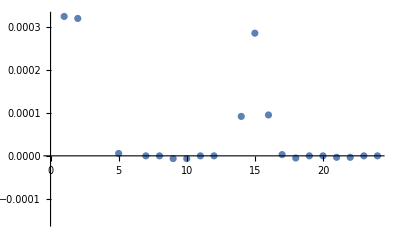

```mathematica
ListPlot[%777]
```

```mathematica
ClearAss[bcf1, bcf2, bcf3, bcf,bc]

bcf1[i_, j_,q_] := Module[{f},If[i == 1,f= -Chi0 listaa[q][[j]] + v0[q]^(2 j)Conjugate[listbbminus[q][[j]]]+TempratureInteraction1[q,j],0]
]
```

```mathematica
ClearAss[bcf1, bcf2, bcf3, bcf,bc]

bcf11[i_, j_,q_] := Module[{f,f1},
f1=-Chi0 listaa[q][[j]] + v0[q]^(2 j)Conjugate[listbbminus[q][[j]]];
f= If[TS==0,f1,f1+TempratureInteraction1[q,j]];
If[i == 1,f,0]
]

bcf21[i_, j_,q_] := Module[{f,f1},
f1 =Chi0 v0[q]^(2j) listaaminus[q][[j]]- Conjugate[listbb[q][[j]]];
f= If[TS==0,f1,f1 +TempratureInteraction2[q,j]];
If[i == 2,f,0]
]

bcf31[i_, j_,q_] := Module[{f},If[i == 3,f =-listaa[q][[j]] - v0[q]^(2 j) Conjugate[listbbminus[q][[j]]],0]
]

bcf41[i_, j_,q_] := Module[{f},If[i == 4,f =- v0[q]^(2 j) listaaminus[q][[j]] - Conjugate[listbb[q][[j]]],0]
]

bcf1[i_, j_,q_]:= Module[{f}, f =( bcf11[i,j,q]+ bcf21[i,j,q]+bcf31[i,j,q]+bcf41[i,j,q])]

ClearAss[bbc1]

bbc1[j_,q_]:=Module[{f}, f=Table[bcf1[j,i,q], {k,1},{i,n}]]
Clear[bc]
```

ClearAss[bcf1,bcf2,bcf3,bcf,bc]

ClearAss[bbc1]

```mathematica
bbc1[j_,q_]:=Module[{f}, f=Table[bcf1[j,i,q], {k,1},{i,n}]]
```

```mathematica
MatrixForm[bbc1[1,1]]
```

(bcf1[1,1,1] | bcf1[1,2,1] | bcf1[1,3,1])

```mathematica
bbc1
```

bbc1

```mathematica
f1=Flatten[Table[0, {q,ntot},{i,n}]]
```

{0,0,0,0,0,0}

```mathematica
Smatr=Simplify[(Re[Smat])];
Smati=Simplify[Im[Smat]];
SmatF=Flatten[{{Smatr},{Smati}}];
```

```mathematica
Smat
```

(Smat1[1,1]
Smat1[1,2]
Smat1[1,3]
Smat1[2,1]
Smat1[2,2]
Smat1[2,3])

```mathematica
MatrixForm[Ffar]
```

(Ffar1[1,1]
Ffar1[1,2]
Ffar1[1,3]
Ffar1[2,1]
Ffar1[2,2]
Ffar1[2,3])

```mathematica
ntot
```

2

```mathematica
Clear[Smnpq1,Smnpq]
Smnpq1[m_,n_,p_,q_]:=Block[{f},f=Smnpq[m,n,p,q]]
```

```mathematica
Smnpq1[1,2,3,4]
```

Smnpq[1,2,3,4]

```mathematica
n,q
```

```mathematica
ndim2
```

3

```mathematica
Clear[ss]
ndim = n*ntot;
ndim2=ndim/2;
ss=ConstantArray[0,{ndim,ndim}];
Clear[i,j,p]
ind=1;
For[q=1,q<ntot+1,q++,
     For[j=1,j<n+1,j ++,

For[p=1,p<=ntot,p++,For[i=1,i<n+1,i++,(*Print["i: ",i," j: ",j," p: ",p," q: ",q];*)If[p==q,Break[]] Clear[jnd];jnd=n*(p-1)+(i-1);
		(*Print["ind: ",ind," jnd: ",jnd];*)

ss[[i,j]]=al[i,j,p,q];
]]



Clear[ind2];ind2=ind;
Clear[ind];ind=ind2+0;

]]
MatrixForm[ss]
Dimensions[ss]
End[]
```

(al[1,1,1,2] | al[1,2,1,2] | al[1,3,1,2] | 0 | 0 | 0
al[2,1,1,2] | al[2,2,1,2] | al[2,3,1,2] | 0 | 0 | 0
al[3,1,1,2] | al[3,2,1,2] | al[3,3,1,2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

{6,6}

End::noctx: No previous context defined.

Global`

```mathematica
Clear[ll]
ndim = 1*n*ntot;
ndim2=ndim/2;
ll=ConstantArray[0,{ndim,ndim}];
Clear[i,j,m]
ind=2;
m=0;
For[q=1,q<ntot+1,q++,
     For[j=1,j<n+1,j ++,

For[p=1,p<=ntot,p++,For[i=1,i<n+1,i++,If[p==q,Break[]] Clear[jnd];jnd=n*(p-1)+(i-1)+1;
m+=1;

ll[[ind-1,jnd]]=a1[i,j,p,q, ind-1,jnd];




]]



Clear[ind2];ind2=ind;
Clear[ind];ind=ind2+1;

]]


MatrixForm[ll]
Dimensions[ll]
```

(0 | 0 | 0 | a1[1,1,2,1,1,4] | a1[2,1,2,1,1,5] | a1[3,1,2,1,1,6]
0 | 0 | 0 | a1[1,2,2,1,2,4] | a1[2,2,2,1,2,5] | a1[3,2,2,1,2,6]
0 | 0 | 0 | a1[1,3,2,1,3,4] | a1[2,3,2,1,3,5] | a1[3,3,2,1,3,6]
a1[1,1,1,2,4,1] | a1[2,1,1,2,4,2] | a1[3,1,1,2,4,3] | 0 | 0 | 0
a1[1,2,1,2,5,1] | a1[2,2,1,2,5,2] | a1[3,2,1,2,5,3] | 0 | 0 | 0
a1[1,3,1,2,6,1] | a1[2,3,1,2,6,2] | a1[3,3,1,2,6,3] | 0 | 0 | 0)

{6,6}

```mathematica
dot=ll.Smat;
Dimensions[dot]
SmatF[[1]](**p, m*)
(*q=1, m=1*)
dot[[2]]
```

{6}

Re[Smat1[1,1]]

a1[1,2,2,1] Smat1[2,1]+a1[2,2,2,1] Smat1[2,2]+a1[3,2,2,1] Smat1[2,3]

```mathematica
Ffar=ConstantArray[0,{ndim}];
For[q=1,q<ntot+1,q++,
     For[j=1,j<n+1,j ++,
ind1=j+n(q-1);
Ffar[[ind1]]=Fn[q][[i]]];
Print[Ffar[[ind1]]]
]
MatrixForm[Ffar]
(*Ffar:=Module[{f,f1},
f1=ll=ConstantArray[0,{ndim,ndim}];
f=Flatten[Table[Ffar1[q,i], {q,ntot},{i,n}]]]*)
Smat:=Flatten[Table[Smat1[q,i], {q,ntot},{i,n}]]
```

23.1543-2.76157 ⅈ

21.6506-8.66025 ⅈ

(23.1543-2.76157 ⅈ
23.1543-2.76157 ⅈ
23.1543-2.76157 ⅈ
21.6506-8.66025 ⅈ
21.6506-8.66025 ⅈ
21.6506-8.66025 ⅈ)

```mathematica
Fn[1]
Fn[2]
```

{23.1543-2.76157 ⅈ}

{21.6506-8.66025 ⅈ}

```mathematica
n
```

3

```mathematica
Table[ReFn[1,i],{i,n}]
Table[ImFn[1,i],{i,n}]
```

Part::partw: Part 2 of {23.1543-2.76157 ⅈ} does not exist.

Part::partw: Part 3 of {23.1543-2.76157 ⅈ} does not exist.

{23.1543,Re[{23.1543-2.76157 ⅈ}⟦2⟧],Re[{23.1543-2.76157 ⅈ}⟦3⟧]}

{ImFn[1,1],ImFn[1,2],ImFn[1,3]}

```mathematica
MatrixForm[Smat]
```

(Smat1[1,1]
Smat1[1,2]
Smat1[1,3]
Smat1[2,1]
Smat1[2,2]
Smat1[2,3])

```mathematica
Fn1[q_,n_]:=Block[{f},f=KroneckerDelta[n,1]dd[q]*Conjugate[gamma]/2.]
Table[Fn1[2,i],{i,n}]
```

{21.6506-8.66025 ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
gamma=50.+I*20;
Fn1[q_]:={dd[q]*Conjugate[gamma]/2.}
ReFn1[q_,n_]:= Module[{f}, f= Re[Fn1[q][[n]]]];
```

```mathematica
Fn1[1]
```

1

```mathematica
Rnq[n_,p_,q_]:=Block[{f,m},f=Sum[smnpq[m,n,p,q]Sm[p,m],{m,1,n}]]

BCTem :=Module[{f,f1,f2},f= -(ThermalConductivityQBar[q]-1)]
```

```mathematica
Fn[1]
```

{23.1543-2.76157 ⅈ}

```mathematica
(*Cass the package that needs to be run!*)
Get["geometry.m"];
Needs["geometry`"];
```

geometry

```mathematica
n
```

3

```mathematica
ReFn1[q_,n_]:= Module[{f}, f= Re[Fn[q,n]]];
ImFn1[q_,n_]:= Module[{f}, f= Im[Fn[q,n]]];
Fn[1,1]
Table[Fn[q,i],{q,ntot},{i,n}]
r=Table[ReFn1[q,i],{q,ntot},{i,n}];
MatrixForm[r]
Dimensions[r]
```

23.1543-2.76157 ⅈ

{{23.1543-2.76157 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{21.6506-8.66025 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

(23.1543 | 0. | 0.
21.6506 | 0. | 0.)

{2,3}

```mathematica
gamma=50.+I*20;
Fn[n_,q_]:=Block[{f},f=KroneckerDelta[n,1]dd[q]*Conjugate[gamma]/2.]
```

SetDelayed::write: Tag Fn in Fn[n_,q_] is Protected.

$Failed

```mathematica
Clear[Ffar]
ndim = n*ntot;
Ffar=ConstantArray[0,{ndim}];
For[q=1,q<ntot+1,q++,
     For[j=1,j<n+1,j ++,
ind1=j+n(q-1);
Ffar[[ind1]]=Fn[j,q]];
Print[Ffar[[ind1]]]
]
MatrixForm[Ffar]
```

0.+0. ⅈ

0.+0. ⅈ

(23.1543-2.76157 ⅈ
0.+0. ⅈ
0.+0. ⅈ
21.6506-8.66025 ⅈ
0.+0. ⅈ
0.+0. ⅈ)

```mathematica
((ThermalConductivityQBar[q]-1)*(1+v0[q]^(2n)));
```

```mathematica
Get["geometry.m"];
Needs["geometry`"];
Get["expansionCoefficients.m"]
Get["abmnpq.m"]
Needs["ExpansionCoefficient`"]
Needs["abmnpq`"]

(*Get["TemperatureInclusions.m"];
Needs["TemperatureInclusions`"];*)
```

geometry

```mathematica
Clear[VecCreate,BCTem1]
(*VecCreate function is a general function that produces a vector by having func[n,q] and return vector named "funcname" which is a (n*ntot)x1 dimension vector in the below form:
 ({{ReFn1[1,1]}, {ReFn1[2,1]}, {ReFn1[3,1]}, {ReFn1[1,2]}, {ReFn1[2,2]}, {ReFn1[3,2]}}). Here we have 2 inclusions and n-the umber of harmonic terms; n is 3 here.*)
VecCreate[funcname_,func_,n_,ntot_]:= Module[{f,ndim,i,j,ind1},
ndim = n*ntot;
ind1=0;
funcname=ConstantArray[0,{ndim}];
f=
For[i=1,i<ntot+1,i++,
     For[j=1,j<n+1,j ++,
ind1=j+n(i-1);
(*Print["i: ", i," j: ",j, " ind1: ",ind1];*)
funcname[[ind1]]=func[j,i]];
]]

(*Test it
Clear[funcname]
VecCreate[funcname,ReFn1,n,ntot]
MatrixForm[funcname]*)


(*MatrixCreate[matname_,Rmnpq_,n_,ntot_]
This function generates a matrix of (n*ntot)x(n*ntot) dimensions with components of R[m,n,p,q] in the below form.Here ntot=2 and n=2.
({{Rmnpq[1,1,1,1], Rmnpq[2,1,1,1], Rmnpq[3,1,1,1], Rmnpq[1,1,2,1], Rmnpq[2,1,2,1], Rmnpq[3,1,2,1]}, {Rmnpq[1,2,1,1], Rmnpq[2,2,1,1], Rmnpq[3,2,1,1], Rmnpq[1,2,2,1], Rmnpq[2,2,2,1], Rmnpq[3,2,2,1]}, {Rmnpq[1,3,1,1], Rmnpq[2,3,1,1], Rmnpq[3,3,1,1], Rmnpq[1,3,2,1], Rmnpq[2,3,2,1], Rmnpq[3,3,2,1]}, {Rmnpq[1,1,1,2], Rmnpq[2,1,1,2], Rmnpq[3,1,1,2], Rmnpq[1,1,2,2], Rmnpq[2,1,2,2], Rmnpq[3,1,2,2]}, {Rmnpq[1,2,1,2], Rmnpq[2,2,1,2], Rmnpq[3,2,1,2], Rmnpq[1,2,2,2], Rmnpq[2,2,2,2], Rmnpq[3,2,2,2]}, {Rmnpq[1,3,1,2], Rmnpq[2,3,1,2], Rmnpq[3,3,1,2], Rmnpq[1,3,2,2], Rmnpq[2,3,2,2], Rmnpq[3,3,2,2]}}).
Also,line If[p==q,Break[]] Clear[jnd]; guarantees if both terms are the same,the matrix element becomes zero.*)
Clear[MatrixCreate,matname]
MatrixCreate[matname_,Amnpq_,n_,ntot_]:=Module[{f, ndim,ndim2,i,j,p,q,m,ind,ind2,jnd},
ndim = 1*n*ntot;
     ndim2=ndim/2;
ind=2;
     m=0;
matname=ConstantArray[0,{ndim,ndim}];
For[q=1,q<ntot+1,q++,
     For[j=1,j<n+1,j ++,

For[p=1,p<=ntot,p++,For[i=1,i<n+1,i++,
(*If[p==q,Break[]] Clear[jnd];*)
jnd=n*(p-1)+(i-1)+1;
m+=1;
(*, ind-1,jnd*)
	matname[[ind-1,jnd]]=Amnpq[i,j,p,q]
];];
Clear[ind2];ind2=ind;
Clear[ind];ind=ind2+1;

];];]

(* Test it by
Clear[matname]
MatrixCreate[matname,Amnpq,2,3]
MatrixForm[matname]
Dimensions[matname]*)

(*This is the reverse of the vector function.It allocates vector terms according to the specific array of n*ntot length.*)
VecRev[funcname_,func_,n_,ntot_]:= Module[{f,ndim,i,j,ind1},
ndim = n*ntot;
ind1=0;
f=
For[i=1,i<ntot+1,i++,
     For[j=1,j<n+1,j ++,
ind1=j+n(i-1);
(*Print["i: ", i," j: ",j, " ind1: ",ind1];*)
func[j,i]=funcname[[ind1]]];
]]

(*This is the attempt to solve the temperature field of many body inclusion problems.I HAVE TO WRITE DOWN EQUATIONS IN THE DOCUMENTATION FILE.*)

-Graphics-
(*The first step to solve the problem is to write fnq as a function of Snq and from that solve the above equation for Snq.Having Snq,fnq and then Gnq can be calculated.From that,we can use these expansion coefficients of temperature fields and derive the temperature terms of the boundary equations.*)
-Graphics-
(*-Graphics-*)

[M1Tem1,M2Tem1,BC1, Mtem1,BCTem1,Tem1,Rmnpq,Rmat]

BCTem1[n_,q_]:=-(ThermalConductivityQBar[q]-1)(Fn[n,q]+Conjugate[Fn[n,q]]*v0[q]^(2n));

RSmnpq[m_,i_,p_,q_]:=Block[{f},f= Eta[[m,Abs[i],p,q]]Exp[-I Theta[p,q]]]


M1Tem1[m_,n_,p_,q_]:=Module[{f,f1,f2},
f1=(ThermalConductivityQBar[q]-1)*smnpq[m,n,p,q];
f2=(ThermalConductivityQBar[q]+(v0[q]^(2n) + v0[q]^(-2n))/(v0[q]^(2n) - v0[q]^(-2n)))*KroneckerDelta[m,n]*KroneckerDelta[p,q];
f=f1+f2]

M2Tem1[m_,n_,p_,q_]:=Module[{f,f1,f2},
f1=(ThermalConductivityQBar[q]-1)*v0[q]^(2n)*Conjugate[smnpq[m,n,p,q]];
f2=(2./(v0[q]^(2n) - v0[q]^(-2n)))*KroneckerDelta[m,n]*KroneckerDelta[p,q];
f=f1+f2]
```

```mathematica
Clear[BCTem,M1Tem,M1TemR,M2Tem]
Clear[Ffar]
VecCreate[Ffar,Fn,n,ntot](*NOT SURE WE NEED IT!*)
VecCreate[BCTem,BCTem1,n,ntot]

MatrixCreate[M1Tem,M1Tem1,n,ntot];
MatrixCreate[M2Tem,M2Tem1,n,ntot];
RealMTem = M1Tem+M2Tem;
ImMTem = M1Tem-M2Tem;
RealBCTem = Re[BCTem];
ImBCTem = Im[BCTem];
real = LinearSolve[RealMTem,RealBCTem ]
im = LinearSolve[ImMTem,ImBCTem ]
(*STem is a vector of Snq terms.
To derive Snq,we need a reverse vector operation.*)
STem= real+I*im

Clear[Snq1,Snq,maxn]
maxn=n;
VecRev[STem,Snq1,n,ntot]
Snq[n_,q_]:=If[n>0 && n<= maxn,Snq1[n,q],0]


(*Snq[n,q]*)

(*First find fnq, then Gnq eq 2.2.9*)
Clear[RSmnpq,fnq,fnq1]

(*fnq1:=Block[{f,f1,f2,Rmnpq},
MatrixCreate[Rmnpq,smnpq,n,ntot];
f1=Rmnpq.STem;
VecRev[f1,f2,n,ntot];
f=f2]*)

Clear[Rmnpq,f1,fnq1];
MatrixCreate[Rmnpq,smnpq,n,ntot];
f1=Rmnpq.STem;
VecRev[f1,fnq1,n,ntot];


fnq[n_,q_]:=If[n>0 && n<= maxn,Fn[n,q]+fnq1[n,q],0]

(*It is not working as f1=Rmnpq.STem; is an array.*)

(*MatrixForm[BC1]
MatrixForm[M1Tem]
MatrixForm[M2Tem]*)

(*Snq[1,1]==STem[[1]]
Snq[2,1]==STem[[2]]
Snq[3,1]==STem[[3]]
Snq[1,2]==STem[[4]]
Snq[2,2]==STem[[5]]
Snq[3,2]==STem[[6]]*)


Gnq[n_,q_]:=(1+1./ThermalConductivityQBar[q])(fnq[n,q] + Snq[n,q])/2. +(1-1./ThermalConductivityQBar[q])Conjugate[fnq[n,q]]v0[q]^(2n)/2.;
```

{43.9458+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{9.97373+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{43.9458+9.97373 ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Get["expansionCoefficients.m"]
Get["abmnpq.m"]
Needs["ExpansionCoefficient`"]
Needs["abmnpq`"]
Clear[Rmnpq]
(*Here we calculate the Rmnpq matrix.*)
MatrixCreate[Rmnpq,smnpq,n,ntot]


M1tem:=-(ThermalConductivityQBar[q]-1)
```

(89.4124+5.332 ⅈ
0.+0. ⅈ
0.+0. ⅈ
84.4375+16.8875 ⅈ
0.+0. ⅈ
0.+0. ⅈ)

```mathematica
Clear[bcTem1nq]
bcTem1nq[n_,q_]:=Module[{f,f1,f2,f3,f4},
f1=Bettal0*dd[q]/n/2.;
f2=-BettalQ[q]*dd[q]/n/2.;
f3=(fnq[n+1,q]-fnq[n-1,q]) + (Snq[n-1,q]-Snq[n+1,q])+Snq[1,q]((-v0[q])^(n));
f4=Gnq[n+1,q]-Gnq[n-1,q];
f=f1*f3+f2*f4]

Clear[bcTem2nq]
bcTem2nq[n_,q_]:=Module[{f,f0,f1,f2,f3,f4},
f0=v0[q]^(2n);
f1=Bettal0*dd[q]/n/2.;
f2=-BettalQ[q]*dd[q]/n/2.;
f3=(fnq[n-1,q]-fnq[n+1,q]) f0+ Snq[1,q]((-v0[q])^(n));
f4=(Gnq[n-1,q]-Gnq[n+1,q]) f0;
f=f1*f3+f2*f4]
```

```mathematica
Clear[bcTem1vec]
VecCreate[bcTem1vec,bcTem1nq,n,ntot]
Clear[bcTem2vec]
VecCreate[bcTem2vec,bcTem2nq,n,ntot]
```

```mathematica
bcTem1vec
bcTem2vec
```

{-0.0000639865-0.0000337177 ⅈ,0.000290412+0.0000461738 ⅈ,-0.0000639865-0.0000337177 ⅈ}

{-0.0000639865-0.0000337177 ⅈ,-0.00189333-0.0000359598 ⅈ,-0.0000639865-0.0000337177 ⅈ}

```mathematica
n
```

3

```mathematica
ntot
```

1